```mathematica
m=5
```

5

```mathematica
A=RandomComplex[{-1-I,1+I},{m,m}];
```

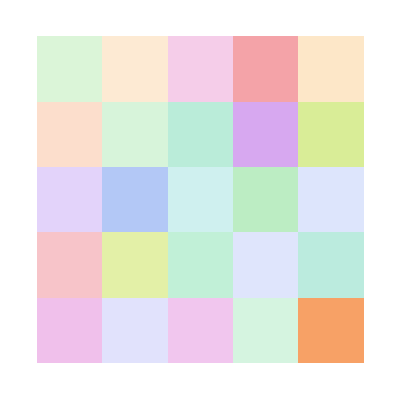

```mathematica
ComplexArrayPlot[A,ImageSize->Tiny]
```

```mathematica
{U,Σ,V}=SingularValueDecomposition[A];
```

```mathematica
Σ//MatrixForm
```

(2.99843 | 0. | 0. | 0. | 0.
0. | 2.50423 | 0. | 0. | 0.
0. | 0. | 1.58692 | 0. | 0.
0. | 0. | 0. | 0.937016 | 0.
0. | 0. | 0. | 0. | 0.0912947)

```mathematica
P=V.ConjugateTranspose[U];
```

```mathematica
B=P.A;
```

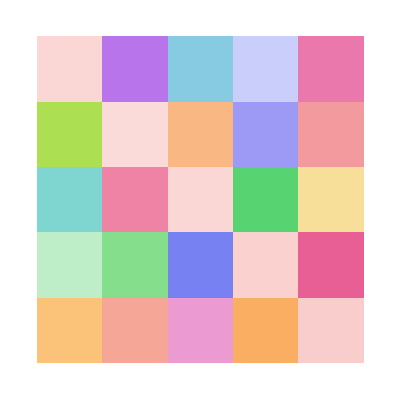

```mathematica
ComplexArrayPlot[B,ImageSize->Tiny]
```

```mathematica
Max[Abs[ConjugateTranspose[B]-B]]
```

1.05069×10^-15